# Make Regular n-gon

This notebook has been created with Mathematica Commercial License L3302-6545 .

June 4, 2020

Copyright (c) David M. Morgan, Ph.D.
GNU General Public License, v. 3.0 or later

Antigonish Landing, NS B2G 2L2 Canada
dmmorgan@gmail.com
(902) 318-4906

Freelance Math and Science Wizardry

Originally developed as a means of teaching myself how to implement rotation matrices in 
Mathematica, I later used the base code to create polygons matching the ages of my children, to use as line-art in custom-made birthday cards.

Algorithm:

1. Request a user-chosen number of vertices n | n ≳ 3, and draw the corresponding n-gon according to the following: 

2. Create vertices, determining them as the {x,y} coordinates of the set of vectors given by rotating an initial vector {0, 1} through angles { (1 (2π))/n, (2 (2π))/n, ..., (n (2π))/n}. Note that this recreates the initial vertex as the last vertex; a choice taken for ease of defining the lines in a later step using Table[]. 

3. Proceeding from vertices 1 and 2, followed by 2 and 3, then by 3 and 4, and so on, define line segments between the coordinates of successive vertices.

Code:

Define a NotebookName. 

Define a preferred working directory and go work in it.

```mathematica
NotebookName = "Make Regular n-gon v Beta.nb";

wd = "/shared/OneDrive/code/mathematica/Commercial/Regular n-gon";
SetDirectory[wd]
```

/shared/OneDrive/code/mathematica/Commercial/Regular n-gon

Ask the user for the desired number of vertices.

```mathematica
numvertices = Input["Draw a polygon with how many sides?" , 9];
If[numvertices < 3, "No! That's not going to work!!!","Phew! A closed object."]
```

Phew! A closed object.

Define an appropriate rotation matrix, one with an iterator that can be used to implement successive stepwise increases in the value of the rotation angle. 

One may consult any standard linear algebra text to confirm that a general, 2-dimensional rotation matrix is: 

	-Graphics-,

in which θ is the angle of rotation, taking positive values to mean clockwise; as indicated above. In this case, θ takes on values i(2 π)/n, in which n = numvertices and i | i ∈ {1, 2, 3, ..., n}.

```mathematica
RR = RotationMatrix[ 2 i Pi / numvertices];
RR//MatrixForm
```

(Cos[(2 i π)/9] | -Sin[(2 i π)/9]
Sin[(2 i π)/9] | Cos[(2 i π)/9])

Compute the vertices.

```mathematica
vertices = Table[
{0,1} . RR,
{i, 0, numvertices}
]
```

{{0,1},{Sin[(2 π)/9],Cos[(2 π)/9]},{Cos[π/18],Sin[π/18]},{(√3)/2,-1/2},{Sin[π/9],-Cos[π/9]},{-Sin[π/9],-Cos[π/9]},{-(√3)/2,-1/2},{-Cos[π/18],Sin[π/18]},{-Sin[(2 π)/9],Cos[(2 π)/9]},{0,1}}

Define lines as those between vertices[[1]] & vertices[[2]], vertices[[2]] & vertices[[3]], vertices[[3]] & vertices[[4]] ... vertices[[-1+Length[vertices]]] & vertices[[Length[vertices]]].  Note this is the justification of the duplication of the initial vertex.

```mathematica
lines = Line[
Table[
{vertices[[i]], vertices[[1+i]]},
{i, 1, -1+Length[vertices]}
]
];
```

Show the object.

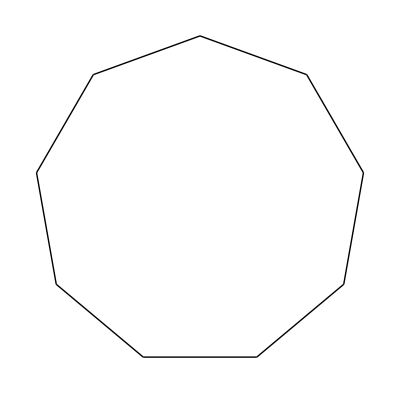

```mathematica
Graphics[lines]
```

Highlight the line containing the duplicated vertex in red.

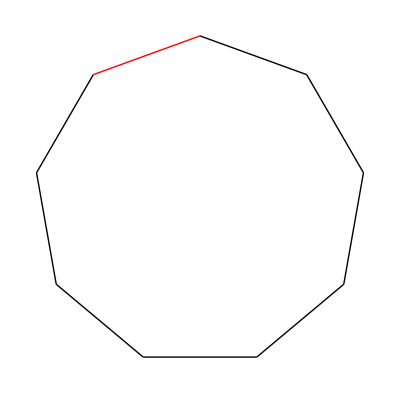

```mathematica
Show[
Graphics[Line[Table[
lines[[1,i]], {i, 1, -1+ numvertices}]]],
Graphics[{Red, Line[lines[[1,numvertices]]]}]
]
```